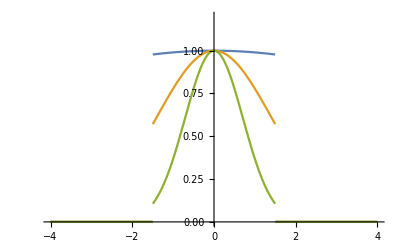

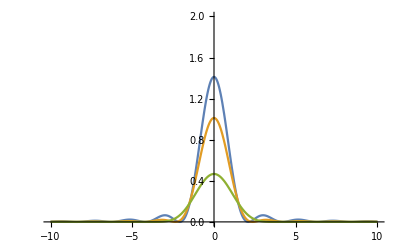

(5 ⅇ^(-25 y^2) (Erf[0.1-(0.+5. ⅈ) y]+Erf[0.1+(0.+5. ⅈ) y]))/(√2)

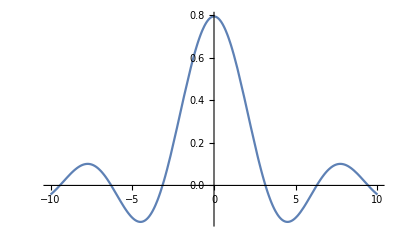

```mathematica
x0=1.5;
f[x_,s_]:=Exp[-x^2/s]*HeavisideTheta[x+x0]*HeavisideTheta[x0-x]
Plot[{f[x,100],f[x,4],f[x,1]},{x,-4,4},PlotRange->{{-4,4},{0,1.2}}]
F1[y_]=FourierTransform[f[x,100],x,y];
F2[y_]=FourierTransform[f[x,4],x,y];
F3[y_]=FourierTransform[f[x,1],x,y];
Plot[{(F1[y])^2,(F2[y])^2,(F3[y])^2},{y,-10,10},PlotRange->{{-10,10},{0,2}}]
```